```mathematica
(*Se van a importar los datos*)
datosAu30lambda=Import["C:\\Users\\Nanoplasmonics\\Documents\\Github\\Tesis-de-Licenciatura\\COMSOL\\Au-sph-30nm-lambda4.csv"];
datosAu30radius=Import["C:\\Users\\Nanoplasmonics\\Documents\\Github\\Tesis-de-Licenciatura\\COMSOL\\Au-sph-30nm-radius10.csv"];
(*Se eliminan los encabezados de los datos*)
datos1Au30lambda=Drop[datosAu30lambda,1];
datos2Au30radius=Drop[datosAu30radius,1];
(*Se pasa de longitudes de onda a energías y se toma a la primera columna como el vector de energías*)
lambdadatosAu30lambda=datos1Au30lambda[[All,1]];
lambdadatosAu30radius=datos2Au30radius[[All,1]];
(*Se interpolan los datos de la parte imaginaria y real*)
au30LambdaCabs=Transpose[{lambdadatosAu30lambda,datos1Au30lambda[[All,2]]*(10^(18))}];
au30RadiusCabs=Transpose[{lambdadatosAu30radius,datos2Au30radius[[All,2]]*(10^(18))}];
au30LambdaCsca=Transpose[{lambdadatosAu30lambda,datos1Au30lambda[[All,3]]*(10^(18))}];
au30RadiusCsca=Transpose[{lambdadatosAu30radius,datos2Au30radius[[All,3]]*(10^(18))}];
```

```mathematica
Length[datos2Au30radius[[All,2]]]
```

151

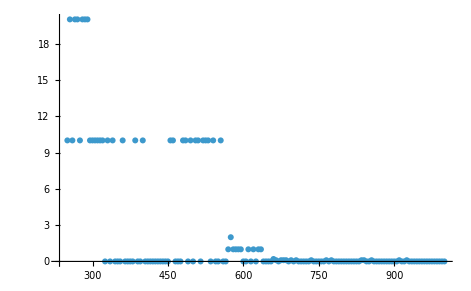

```mathematica
(*Diferencia entre el tamaño del PML: agregar los tiempos de cómputo*)
ListPlot[Transpose[{lambdadatosAu30lambda,Abs[datos1Au30lambda[[All,2]]*(10^(18))-datos2Au30radius[[All,2]]*(10^(18))]}]]
```

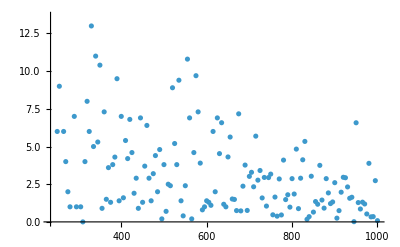

```mathematica
ListPlot[Transpose[{lambdadatosAu30lambda,Abs[datos1Au30lambda[[All,3]]*(10^(18))-datos2Au30radius[[All,3]]*(10^(18))]}]]
```

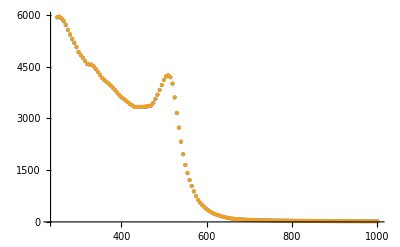

```mathematica
ListPlot[{au30LambdaCabs,au30RadiusCabs}]
```

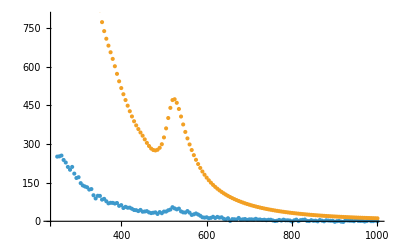

```mathematica
ListPlot[{au30LambdaCsca,auCscaMie}]
```

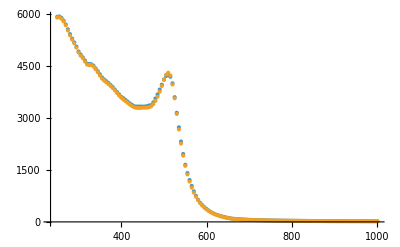

```mathematica
ListPlot[{au30LambdaCabs,auCabsMie}]
```

```mathematica
Length[au30LambdaCabs[[All,2]]]
Length[auCabsMie[[All,2]]]
```

151

161

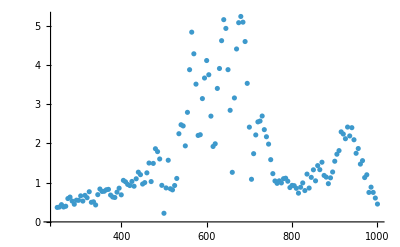

```mathematica
ListPlot[Transpose[{lambdadatosAu30lambda,(Abs[au30LambdaCabs[[All,2]]-auCabsMie[[All,2]]]/au30LambdaCabs[[All,2]])*100}]]
```